```mathematica
monopole[x_,y_] := Exp[-(x^2+y^2)];
dipole[x_,y_] := x Exp[-(x^2+y^2)];
quadrupole[x_,y_] := x  y Exp[-(x^2+y^2)];
```

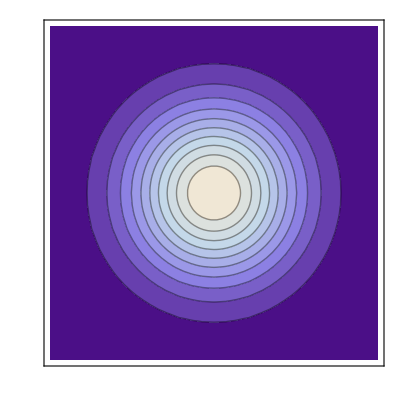

```mathematica
ContourPlot[monopole[x,y],{x,-2,2},{y,-2,2}, Contours->10,ClippingStyle->Automatic,FrameTicks->None]
```

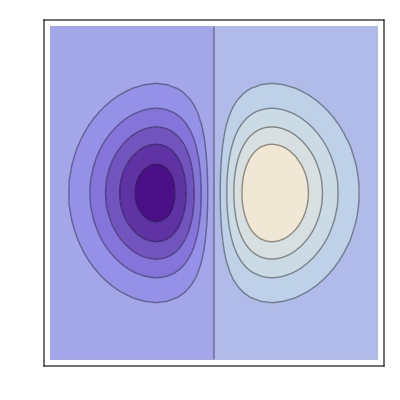

```mathematica
ContourPlot[dipole[x,y],{x,-2,2},{y,-2,2}, Contours->10, ClippingStyle->Automatic,FrameTicks->None]
```

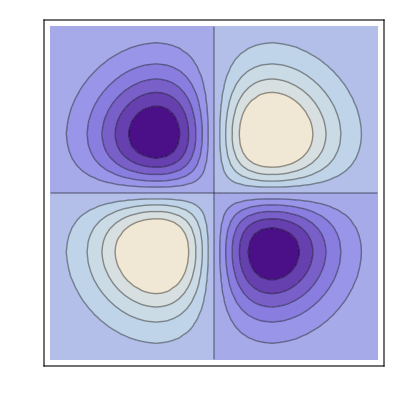

```mathematica
ContourPlot[quadrupole[x,y],{x,-2,2},{y,-2,2}, Contours->10, ClippingStyle->Automatic,FrameTicks->None]
```